51

NonlinearModelFit::nrlnum: The function value {-10483.7 - 0.126026\ ⅈ, -10356.5 - 0.126026\ ⅈ, -10504.6 - 0.126026\ ⅈ, -12969.9 - 0.126026\ ⅈ, -10268.8 - 0.126026\ ⅈ, -10001.3 - 0.126026\ ⅈ, « 39 », -10.7313 - 0.129877\ ⅈ, -5.94318 - 0.130591\ ⅈ, -4.44105 - 0.131142\ ⅈ, -2.6683 - 0.132098\ ⅈ, -1.14729 - 0.134121\ ⅈ, « 1 »} is not a list of real numbers with dimensions {51} at {a, alpha} = {-82.9862, 138.131}.

FittedModel::varnum: The estimated variance 3.70231×10^7 + 1039.45\ ⅈ is not a positive number. Properties requiring division by the variance or standard error will not be computed.

Missing[]

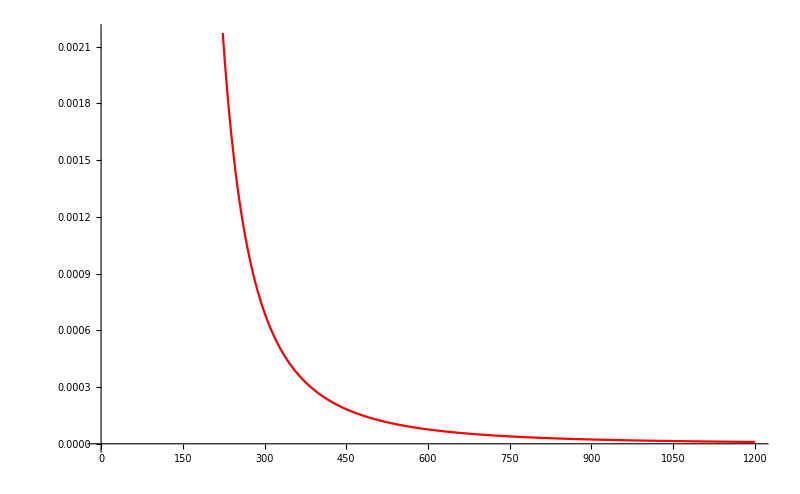

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["datos2_ready.dat"];
L=Length[data];
51
(*M = 2.0;
gamma =2.0;
a = 1.2;*)
Ip[R_]:=Piecewise[{{alpha*((2+(R/a)^2)*(Log[(1+Sqrt[1-(R/a)^2])/(R/a)]/(Sqrt[1-(R/a)^2]))-3)/(a^2*(1-(R/a)^2)^2),R<a},{2*alpha/(7.5*a*a),R==a},{alpha*((2+(R/a)^2)*(ArcCos[1/(R/a)]/Sqrt[(R/a)^2-1])-3)/(a^2*(1-(R/a)^2)^2),R>a}}];
(*Plot[Ip[R],{R,0,4}]*)
fit = NonlinearModelFit[data,Ip[R],{a,alpha},R,MaxIterations->10000];
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,0,1200},PlotStyle->Red,Epilog:>Point[data],ImageSize->800]
```